# s-Matrix of QH setup and unitarity of s-matrix

## Energy-independent scattering amplitudes and probabilities

```mathematica
τ=√T;
ρ=√(1-T);
mat1={{0,τ Exp[I α],0,-I ρ Exp[I α]},{0,0,Exp[I χ2],0},{0,-I ρ Exp[I α],0,τ Exp[I α]},{Exp[I χ1],0,0,0}};
Re[mat1.Transpose[Conjugate[mat1]]/.{T->0.2,α->π/4,χ1->1,χ2->1}]
```

{{1.,0,0.,0},{0,1,0,0},{0.,0,1.,0},{0,0,0,1}}

## Energy-dependent (QPC) scattering amplitudes and probabilities

```mathematica
τ=√T;
ρ=√(1-T);
T=1/(1+Exp[-2π(G-10/2)/(0.5*10)]);(*QPC transmission probability*)
mat1={{0,τ Exp[I α],0,-I ρ Exp[I α]},{0,0,Exp[I χ2],0},{0,-I ρ Exp[I α],0,τ Exp[I α]},{Exp[I χ1],0,0,0}};
Re[mat1.Transpose[Conjugate[mat1]]/.{G->6,α->π/4,χ1->1,χ2->1}]
```

{{1.,0,0.,0},{0,1,0,0},{0.,0,1.,0},{0,0,0,1}}

# s-matrix of QSH setup with Helical edge modes and unitarity of the s-matrix

## Energy-independent scattering amplitudes and probabilities

```mathematica
ρ=√(1-T);
τ=√T;
θ=ArcTan[ρ/τ];
ξ=α-θ;
mat1={{0,-I √p Exp[I*ξ],τ √(1-p)Exp[I*α],0,0,0,-I ρ √(1-p)Exp[I*α],0},{-I √p,0,0,0,0,0,0,√(1-p)Exp[I χ1]},{0,0,0,-I √p,√(1-p)Exp[I χ2],0,0,0},{0,τ √(1-p)Exp[-I*α],-I √p Exp[-I*ξ],0,0,I ρ √(1-p)Exp[-I*α],0,0},{0,0,-I ρ √(1-p)Exp[I*α],0,0,-I √p Exp[I*ξ],τ √(1-p)Exp[I*α],0},{0,0,0,√(1-p)Exp[-I χ2],-I √p,0,0,0},{√(1-p)Exp[-I χ1],0,0,0,0,0,0,-I √p},{0,I ρ √(1-p)Exp[-I*α],0,0,0,τ √(1-p)Exp[-I*α],-I √p Exp[-I*ξ],0}};
Re[mat1.Transpose[Conjugate[mat1]]/.{T->0.2,p->0.0,α->π/4,χ1->1,χ2->1}]
```

{{1.,0,0,0.,0.,0,0,0.},{0,1.,0,0,0,0,0.,0},{0,0,1.,0,0,0.,0,0},{0.,0,0,1.,0.,0,0,0.},{0.,0,0,0.,1.,0,0,0.},{0,0,0.,0,0,1.,0,0},{0,0.,0,0,0,0,1.,0},{0.,0,0,0.,0.,0,0,1.}}

## Energy-dependent (QPC) scattering amplitudes and probabilities

```mathematica
ρ=√(1-T);
τ=√T;
θ=ArcTan[ρ/τ];
ξ=α-θ;
T=1/(1+Exp[-2π(G-10/2)/(0.5*10)]);(*QPC transmission probability*)
mat1={{0,-I √p Exp[I*ξ],τ √(1-p)Exp[I*α],0,0,0,-I ρ √(1-p)Exp[I*α],0},{-I √p,0,0,0,0,0,0,√(1-p)Exp[I χ1]},{0,0,0,-I √p,√(1-p)Exp[I χ2],0,0,0},{0,τ √(1-p)Exp[-I*α],-I √p Exp[-I*ξ],0,0,I ρ √(1-p)Exp[-I*α],0,0},{0,0,-I ρ √(1-p)Exp[I*α],0,0,-I √p Exp[I*ξ],τ √(1-p)Exp[I*α],0},{0,0,0,√(1-p)Exp[-I χ2],-I √p,0,0,0},{√(1-p)Exp[-I χ1],0,0,0,0,0,0,-I √p},{0,I ρ √(1-p)Exp[-I*α],0,0,0,τ √(1-p)Exp[-I*α],-I √p Exp[-I*ξ],0}};
Re[mat1.Transpose[Conjugate[mat1]]/.{G->6,p->0.0,α->π/4,χ1->1,χ2->1}]
```

{{1.,0,0,0.,0.,0,0,0.},{0,1.,0,0,0,0,0.,0},{0,0,1.,0,0,0.,0,0},{0.,0,0,1.,0.,0,0,0.},{0.,0,0,0.,1.,0,0,0.},{0,0,0.,0,0,1.,0,0},{0,0.,0,0,0,0,1.,0},{0.,0,0,0.,0.,0,0,1.}}

# s-matrix of QSH setup with Trivial Edge modes and unitarity of the s-matrix

## Energy-independent scattering amplitudes and probabilities

```mathematica
ρ=√(1-T);
τ=√T;
θ=ArcTan[ρ/τ];
ξ=α-θ;
mat1={{0,-I √p Exp[I*ξ],τ √(1-p)Exp[I*α],0,0,0,-I ρ √(1-p)Exp[I*α],0},{-I √p,0,0,0,0,0,0,√(1-p)Exp[I χ1]},{0,0,0,-I √p,√(1-p)Exp[I χ2],0,0,0},{0,τ √(1-p)Exp[-I*α],-I √p Exp[-I*ξ],0,0,I ρ √(1-p)Exp[-I*α],0,0},{0,0,-I ρ √(1-p)Exp[I*α],0,0,-I √p Exp[I*ξ],τ √(1-p)Exp[I*α],0},{0,0,0,√(1-p)Exp[-I χ2],-I √p,0,0,0},{√(1-p)Exp[-I χ1],0,0,0,0,0,0,-I √p},{0,I ρ √(1-p)Exp[-I*α],0,0,0,τ √(1-p)Exp[-I*α],-I √p Exp[-I*ξ],0}};
Re[mat1.Transpose[Conjugate[mat1]]/.{T->0.2,p->0.5,α->π/4,χ1->1,χ2->1}]
```

{{1.,0,0,0.,0.,0,0,0.},{0,1.,0,0,0,0,0.,0},{0,0,1.,0,0,0.,0,0},{0.,0,0,1.,0.,0,0,0.},{0.,0,0,0.,1.,0,0,0.},{0,0,0.,0,0,1.,0,0},{0,0.,0,0,0,0,1.,0},{0.,0,0,0.,0.,0,0,1.}}

## Energy-dependent (QPC) scattering amplitudes and probabilities

```mathematica
ρ=√(1-T);
τ=√T;
θ=ArcTan[ρ/τ];
ξ=α-θ;
T=1/(1+Exp[-2π(G-10/2)/(0.5*10)]);(*QPC transmission probability*)
mat1={{0,-I √p Exp[I*ξ],τ √(1-p)Exp[I*α],0,0,0,-I ρ √(1-p)Exp[I*α],0},{-I √p,0,0,0,0,0,0,√(1-p)Exp[I χ1]},{0,0,0,-I √p,√(1-p)Exp[I χ2],0,0,0},{0,τ √(1-p)Exp[-I*α],-I √p Exp[-I*ξ],0,0,I ρ √(1-p)Exp[-I*α],0,0},{0,0,-I ρ √(1-p)Exp[I*α],0,0,-I √p Exp[I*ξ],τ √(1-p)Exp[I*α],0},{0,0,0,√(1-p)Exp[-I χ2],-I √p,0,0,0},{√(1-p)Exp[-I χ1],0,0,0,0,0,0,-I √p},{0,I ρ √(1-p)Exp[-I*α],0,0,0,τ √(1-p)Exp[-I*α],-I √p Exp[-I*ξ],0}};
A1=Re[mat1.Transpose[Conjugate[mat1]]/.{G->6,p->0.5,α->π/4,χ1->1,χ2->1}];
A2=Chop[A1,10^-10]
```

{{1.,0,0,0,0,0,0,0},{0,1.,0,0,0,0,0,0},{0,0,1.,0,0,0,0,0},{0,0,0,1.,0,0,0,0},{0,0,0,0,1.,0,0,0},{0,0,0,0,0,1.,0,0},{0,0,0,0,0,0,1.,0},{0,0,0,0,0,0,0,1.}}

# Calculation of thermovoltage in QSH setup with topological helical edge modes for different values of QPC energy

```mathematica
T1[G_,x_,y_]:=1/(1+Exp[-2 π (G-10*x/2)/(y*10)])

df[G_]:=Exp[G/10]/((Exp[G/10]+1)^2*10)

Vth[dt_?NumericQ,x_?NumericQ,y_?NumericQ]:=(NIntegrate[(1-2*T1[G,x,y])*G*df[G],{G,-100,100}]*dt)/(2*10*NIntegrate[T1[G,x,y]*df[G],{G,-100,100}])
```

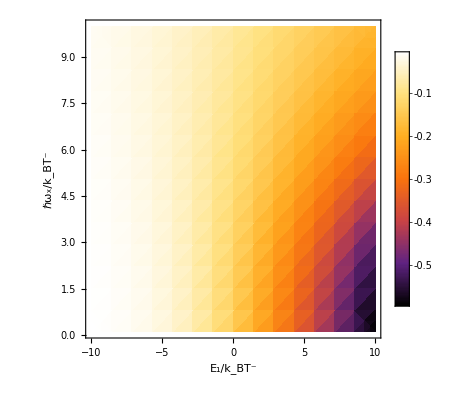

```mathematica
A1=DensityPlot[Vth[1,x,y]/10,{x,-10,10},{y,0.1,10},PlotRange->All,PlotLegends->Automatic,ColorFunction->"SunsetColors",FrameLabel->{Style["E_1/k_BT^-",24,Bold,Black],Style["ℏω_x/k_BT^-",24,Bold,Black]},LabelStyle->Directive[Bold,Black,15],PlotRange->{{-10,10},{-10,10},All},ClippingStyle->Automatic,Frame->True]
```

```mathematica
Export["C:\\Users\\DELL\\Downloads\\fig16.pdf",A1,"PDF"]
```

C:\Users\DELL\Downloads\fig16.pdf

```mathematica
T2[G1_,x_,y_]:=1/(1+Exp[-2 π (G1-x/2)/(y)])
f1[G1_,dt_,x_,y_]:=1/(1+Exp[(G1-Vth[dt,x,y]/10)/(1+dt/2)]);
f2[G1_,dt_]:=1/(1+Exp[G1/(1-dt/2)]);
D1[dt_?NumericQ,x_?NumericQ,y_?NumericQ]:=NIntegrate[T2[G1,x,y](1-T2[G1,x,y])(f1[G1,dt,x,y]-f2[G1,dt])^2,{G1,-∞,∞}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

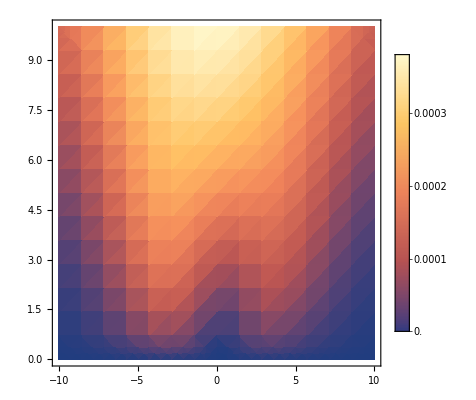

```mathematica
DensityPlot[D1[0.1,x,y],{x,-10,10},{y,0,10},PlotRange->All,PlotLegends->Automatic]
```

# Plot of Δ_T^22 in chiral and helical setup with QPC

```mathematica
Legended[Plot[{0,D1[dt,1,8]},{dt,0,0.1},PlotRange->{{0,0.1},{0.0004,-0.00002}},Exclusions->None,AxesOrigin->{0.0,0.0000},PlotStyle->{{Red,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]},{Brown,AbsoluteThickness[5]},{Yellow,AbsoluteThickness[5]}},PlotLegends->Placed[{Style["",45,Black],Style["",45,Black]},{Left,Center}],FrameTicks->{{{{0.0004,"0.4"},{0.0002,"0.2"},{0,"0.00"}},None},{{{0,"0.0"},{0.05,"0.05"},{0.1,"0.1"}},None}},FrameLabel->{Style["",45,Bold,Black],Style[Rotate["",270 Degree],45,Black]},FrameStyle->Directive[Black,Thickness[0.002]],FrameTicksStyle->Directive["Label",Black,45],ImageSize->1500,Frame->True],{Placed[Style["× 10^-3",45,Black],{{0.22,1.0}}]}]
```

-Graphics-

# Plot of Δ_T^22 (same as Δ_T^44) noise for trivial and topological helical edge mode.

```mathematica
A1=Legended[Plot[{(1+0.5)p(1-p)(π^2/18-1/3)x^2+(1-0.5)p(1-p)(π^2/18-1/3)x^2/.{p->0},(1+0.5)p(1-p)(π^2/18-1/3)x^2+(1-0.5)p(1-p)(π^2/18-1/3)x^2/.{p->0.3},(1+0.5)p(1-p)(π^2/18-1/3)x^2+(1-0.5)p(1-p)(π^2/18-1/3)x^2/.{p->0.6},(1+0.5)p(1-p)(π^2/18-1/3)x^2+(1-0.5)p(1-p)(π^2/18-1/3)x^2/.{p->0.9}},{x,0,0.1},PlotRange->{{0,0.1},{0.0012,-0.00004}},AxesOrigin->{0.0,-0.00004},Exclusions->None,PlotStyle->{{Red,AbsoluteThickness[5]},{Blue,AbsoluteThickness[5]},{Brown,AbsoluteThickness[5]},{Green,AbsoluteThickness[5]}},PlotLegends->Placed[{Style["",45,Black],Style["",45,Black],Style["",45,Black],Style["",45,Black]},{Left,Center}],FrameLabel->{Style["",45,Bold,Black],Style[Rotate["",270 Degree],45,Black]},FrameStyle->Directive[Black,Thickness[0.002]],FrameTicks->{{{{0.0006,"0.60"},{0.0012,"1.20"},{0,"0.00"}},None},{{{0.1,"0.10"},{0.05,"0.05"},{0,"0.00"}},None}},FrameTicksStyle->Directive["Label",Black,45],ImageSize->1500,Frame->True],{Placed[Style["× 10^-3",45,Black],{{0.22,1.0}}]}]
```

-Graphics-